First we need to normalize the 0th and 1th wave functions by determining c_0 and c_1. These just come from doing normalization integrals.

Here is c_0 and ψ_0(x):

```mathematica
cnot = 1/Pi^(1/4); psinot[x_]:= cnot * Exp[-x^2/2]
```

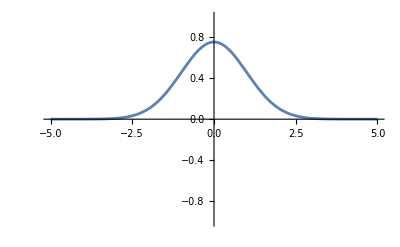

```mathematica
Plot[psinot[x],{x, -5, 5}, PlotRange->{{-5, 5}, {-1, 1}}]
```

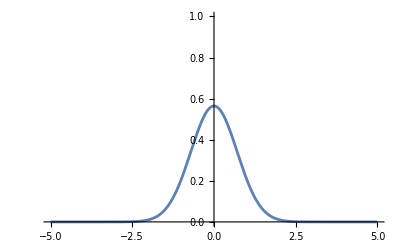

```mathematica
Plot[psinot[x]^2,{x, -5, 5}, PlotRange->{{-5, 5}, {0, 1}}]
```

Here is c_1 and ψ_1(x):

```mathematica
cone = 2^(1/2)/Pi^(1/4); psione[x_]:= cone * x * Exp[-x^2/2]
```

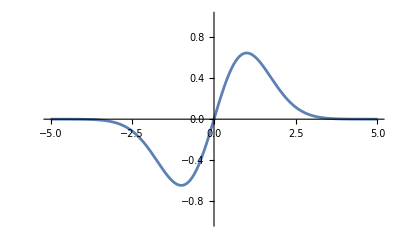

```mathematica
Plot[psione[x],{x, -5, 5}, PlotRange->{{-5, 5}, {-1, 1}}]
```

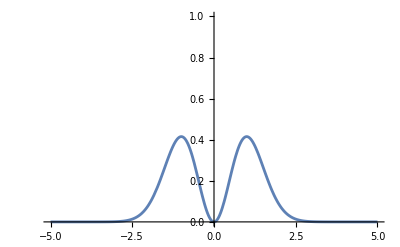

```mathematica
Plot[psione[x]^2,{x, -5, 5}, PlotRange->{{-5, 5}, {0, 1}}]
```

What are we going to do next?

We have ψ_0(x) and ψ_1(x) and now we need to make the combination

ψ(x,t)=(e^(-i E_0 t/ℏ)ψ_0(x) +e^(-i E_1 t/ℏ)ψ_1(x))/(√2)

But that is a probability amplitude. To understand the probability, we also have to take absolute-value sqared of this thing, which means we first have to turn

e^(-i E_0 t/ℏ)=cos(E_0 t)/ℏ-isin(E_0 t)/ℏ

e^(-i E_1 t/ℏ)=cos(E_1 t)/ℏ-isin(E_1 t)/ℏ

and then take the real and imaginary parts of the combinations and square them.

The upshot is

(|ψ(x,t)|)^2=[cos(E_0 t)/ℏ ψ_0(x)+cos(E_1 t)/ℏ ψ_1(x)]^2+[sin(E_0 t)/ℏ ψ_0(x)+sin(E_1 t)/ℏ ψ_1(x)]^2

```mathematica
enot = 1/2; eone = 3/2;
```

```mathematica
timeDependentProbability[x_,t_]:= ((Cos[enot * t]*psinot[x]+Cos[eone * t]*psione[x])^2+(Sin[enot * t]*psinot[x]+Sin[eone * t]*psione[x])^2)/2
```

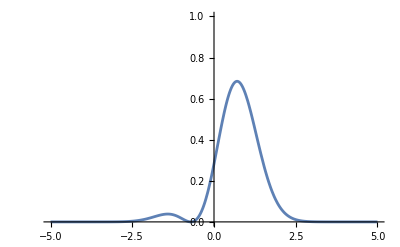

```mathematica
Plot[timeDependentProbability[x,0], {x, -5, 5}, PlotRange->{{-5, 5}, {0, 1}}]
```

```mathematica
Animate[Plot[timeDependentProbability[x,t], {x, -5, 5}, PlotRange->{{-5, 5}, {0, 1}}], {t, 0, 4*Pi}]
```